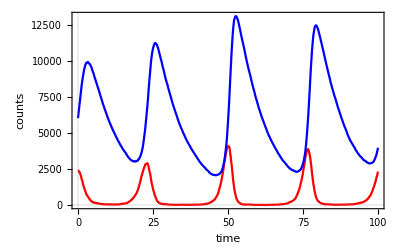
-Graphics- |

```mathematica
SetDirectory[NotebookDirectory[]];
countsP=Import["data/P.txt","Table"];
countsH=Import["data/H.txt","Table"];

leg=LineLegend[{Red,Blue},{"Prey","Hunter"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];

plt=Grid[{{
Show[
ListLinePlot[{countsP,countsH},FrameLabel->{"time","counts"},PlotStyle->{Red,Blue}]
],
leg}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figure.jpg",plt,ImageResolution->200]
```

figure.jpg